# IEEE 802.15.4

## Notes on Travis Goodspeed’s Phantom Boundaries and Cross-Layer Illusions in 802.15.4 Digital Radio

```mathematica
Needs["PlotLegends`"]
```

## Get chips from standards PDF

```mathematica
table24={First[#],Take[#,{2,5}],Drop[#,5]}&/@{{0,0,0,0,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0},{1,1,0,0,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0},{2,0,1,0,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0},{3,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1},{4,0,0,1,0,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1},{5,1,0,1,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0},{6,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1},{7,1,1,1,0,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1},{8,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1},{9,1,0,0,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1},{10,0,1,0,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1},{11,1,1,0,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0},{12,0,0,1,1,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0},{13,1,0,1,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1},{14,0,1,1,1,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0},{15,1,1,1,1,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0}}
```

{{0,{0,0,0,0},{1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0}},{1,{1,0,0,0},{1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0}},{2,{0,1,0,0},{0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0}},{3,{1,1,0,0},{0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1}},{4,{0,0,1,0},{0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1}},{5,{1,0,1,0},{0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1,1,1,0,0}},{6,{0,1,1,0},{1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,0,1}},{7,{1,1,1,0},{1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,1,0,1,1,0,1}},{8,{0,0,0,1},{1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1}},{9,{1,0,0,1},{1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1}},{10,{0,1,0,1},{0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1}},{11,{1,1,0,1},{0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0}},{12,{0,0,1,1},{0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,0}},{13,{1,0,1,1},{0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0,1,0,0,1}},{14,{0,1,1,1},{1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0,1,1,0,0}},{15,{1,1,1,1},{1,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,0,0}}}

```mathematica
MatrixForm[chips=Last/@table24]
```

(1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0)

## Hamming distance, unshifted

```mathematica
MatrixForm[UnshiftedHammingDistance=Outer[HammingDistance,#,#,1]&[chips]]
```

(0 | 16 | 18 | 20 | 20 | 20 | 18 | 16 | 16 | 12 | 14 | 20 | 20 | 20 | 14 | 12
16 | 0 | 16 | 18 | 20 | 20 | 20 | 18 | 12 | 16 | 12 | 14 | 20 | 20 | 20 | 14
18 | 16 | 0 | 16 | 18 | 20 | 20 | 20 | 14 | 12 | 16 | 12 | 14 | 20 | 20 | 20
20 | 18 | 16 | 0 | 16 | 18 | 20 | 20 | 20 | 14 | 12 | 16 | 12 | 14 | 20 | 20
20 | 20 | 18 | 16 | 0 | 16 | 18 | 20 | 20 | 20 | 14 | 12 | 16 | 12 | 14 | 20
20 | 20 | 20 | 18 | 16 | 0 | 16 | 18 | 20 | 20 | 20 | 14 | 12 | 16 | 12 | 14
18 | 20 | 20 | 20 | 18 | 16 | 0 | 16 | 14 | 20 | 20 | 20 | 14 | 12 | 16 | 12
16 | 18 | 20 | 20 | 20 | 18 | 16 | 0 | 12 | 14 | 20 | 20 | 20 | 14 | 12 | 16
16 | 12 | 14 | 20 | 20 | 20 | 14 | 12 | 0 | 16 | 18 | 20 | 20 | 20 | 18 | 16
12 | 16 | 12 | 14 | 20 | 20 | 20 | 14 | 16 | 0 | 16 | 18 | 20 | 20 | 20 | 18
14 | 12 | 16 | 12 | 14 | 20 | 20 | 20 | 18 | 16 | 0 | 16 | 18 | 20 | 20 | 20
20 | 14 | 12 | 16 | 12 | 14 | 20 | 20 | 20 | 18 | 16 | 0 | 16 | 18 | 20 | 20
20 | 20 | 14 | 12 | 16 | 12 | 14 | 20 | 20 | 20 | 18 | 16 | 0 | 16 | 18 | 20
20 | 20 | 20 | 14 | 12 | 16 | 12 | 14 | 20 | 20 | 20 | 18 | 16 | 0 | 16 | 18
14 | 20 | 20 | 20 | 14 | 12 | 16 | 12 | 18 | 20 | 20 | 20 | 18 | 16 | 0 | 16
12 | 14 | 20 | 20 | 20 | 14 | 12 | 16 | 16 | 18 | 20 | 20 | 20 | 18 | 16 | 0)

```mathematica
hue32=Hue[#/32]&
```

Hue[#1/32]&

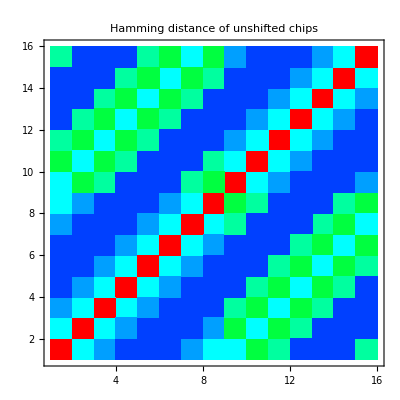

```mathematica
ListDensityPlot[UnshiftedHammingDistance,InterpolationOrder->0,ColorFunction->hue32,ColorFunctionScaling->False,PlotLabel->"Hamming distance of unshifted chips"]
```

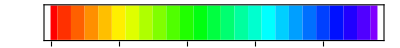

```mathematica
ListDensityPlot[{#,0,#}&/@Range[0,24],InterpolationOrder->0,ColorFunction->hue32,ColorFunctionScaling->False,FrameTicks->{Automatic,None},AspectRatio->1/25,PlotLabel->"Legend",FrameLabel->{"Hamming distance",""}]
```

```mathematica
ListPlot3D[UnshiftedHammingDistance]
```

-Graphics3D-

## Hamming distance with cyclic shifts

```mathematica
Dimensions[chips]
```

{16,32}

```mathematica
Dimensions[cyclicchips=Function[chip,RotateLeft[chip,#]&/@(Range[Length[chip]]-1)]/@chips]
```

{16,32,32}

```mathematica
Dimensions[cyclichammings=Outer[HammingDistance,chips,cyclicchips,1,2]]
```

{16,16,32}

```mathematica
MatrixForm[cyclichammings⟦1⟧]
```

(0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18
16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18
18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20
20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14
20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18
20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12 | 18 | 20 | 16 | 12
18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16 | 16 | 18 | 16 | 12
16 | 18 | 16 | 12 | 18 | 20 | 16 | 12 | 20 | 14 | 14 | 18 | 20 | 18 | 14 | 14 | 20 | 12 | 16 | 20 | 18 | 12 | 16 | 18 | 16 | 16 | 18 | 18 | 0 | 18 | 18 | 16
16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14
12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14
14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12
20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18
20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18
20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16 | 14 | 20 | 16 | 16
14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20 | 12 | 18 | 16 | 16
12 | 18 | 16 | 16 | 14 | 20 | 16 | 16 | 20 | 14 | 14 | 18 | 20 | 14 | 14 | 18 | 20 | 16 | 16 | 12 | 14 | 16 | 16 | 14 | 12 | 12 | 18 | 14 | 16 | 18 | 18 | 20)

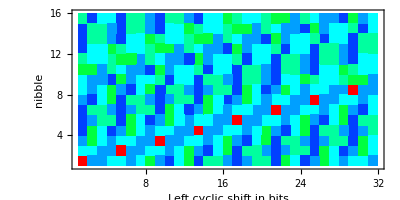

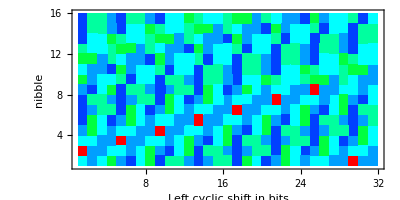

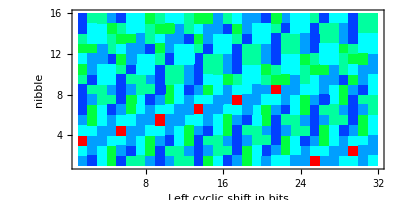

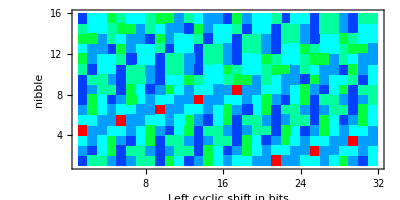

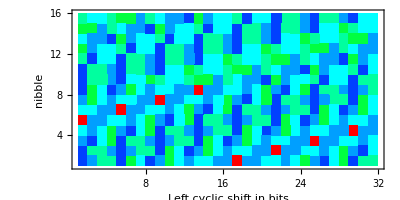

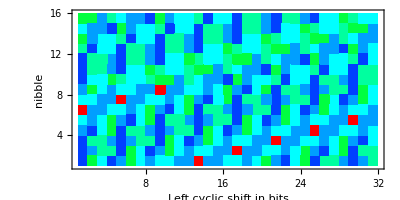

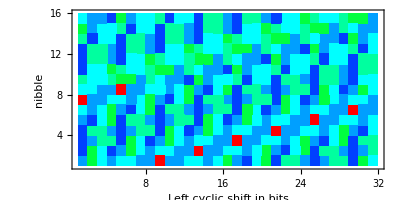

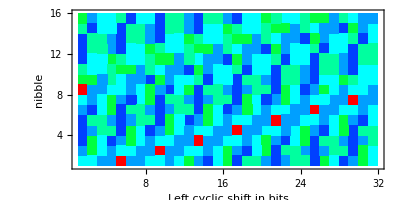

```mathematica
Print[ListDensityPlot[#,ColorFunction->hue32,InterpolationOrder->0,ColorFunctionScaling->False,AspectRatio->1/2,PlotRange->All,FrameLabel->{"Left cyclic shift in bits","nibble"}]]&/@cyclichammings;
```